# Anharmonic Perturbations Last Updated: 2/16/2021

## 1 Get eigen

```mathematica
Remove["Global`*"]
```

## 1.1 Get normal mode data

```mathematica
kM =Append[ Array[k,{2,2}],{kz,kz}];kM=Transpose[Table[If[m[[i]]===m0,kM[[1;;,1]],kM[[1;;,2]]],{i,Num}]];
xM = Array[x,{3,Num}];
	(*Calculate equilibrium positions (axial crystal)*)
z0M = Array[z0,Num];
L0EQ [i_]:=z0M[[i]]==(Sum[(z0M[[i]] - z0M[[k]])^(-2),{k,1,i-1}] - Sum[(z0M[[i]] - z0M[[k]])^(-2),{k, i+1,Num}])
L0EQlist =L0EQ/@Range[Num]//FullSimplify;z0M=z0M/.NSolve[L0EQlist,z0M, Reals][[1]];
L0Mn[i_,j_,n_]:=If[i==j,0,Abs[z0M[[i]]-z0M[[j]]]^n]
	(*Create matrix*)
ke2=2.306569*^-28;l0=(ke2/kz)^(1/3);
ics=ArrayReshape[Append[Table[xM[[d,i]]->0,{d,2},{i,Num}],Table[(xM[[3,i]]-xM[[3,j]])->L0Mn[i,j,1]*l0,{i,Num},{j,i+1,Num}]],{Num*(Num+3)/2}];
Uel=Total[0.5*kM*(xM^2),2]+ke2*Sum[(Total[(xM[[;;,i]]-xM[[;;,j]])^2])^(-0.5),{i,Num},{j,i+1,Num}];
Vel1=-Table[D[Uel,{xM[[d,i]]},{xM[[d,j]]}]/Sqrt[m[[i]]*m[[j]]],{d,3},{i,Num},{j,Num}]/.ics//FullSimplify;
Vel1norm=Vel1/.{m1->m0,k[1,2]->k[1,1],k[2,2]->k[2,1]}//FullSimplify;
```

```mathematica
SetAttributes[{m0,m1,kz},Constant];
m={m0,m1};(*Enter chain configuration here: 1 is lower mass ion, a is higher mass ion*)
wmhz=2*Pi*1*^6;Num =Length[m]; 
kM =Append[ Array[k,{2,2}],{kz,kz}];kM=Transpose[Table[If[m[[i]]===m0,kM[[1;;,1]],kM[[1;;,2]]],{i,Num}]];xM = Array[x,{3,Num}];
		(*1.1.2 Calculate Equilibrium Positions (axial crystal)*)
z0M = Array[z0,Num];
L0EQ [i_]:=z0M[[i]]==(Sum[(z0M[[i]] - z0M[[k]])^(-2),{k,1,i-1}] - Sum[(z0M[[i]] - z0M[[k]])^(-2),{k, i+1,Num}])
L0EQlist = Table[L0EQ[i],{i,Num}] //FullSimplify;z0M=z0M/.NSolve[L0EQlist,z0M, Reals][[1]];
L0Mn[i_,j_,n_]:=If[i==j,0,Abs[z0M[[i]]-z0M[[j]]]^n]
		(*1.1.3 Subbing in mass & secular frequency values*)
m0=138*1.66054*^-27;m1hold=171*1.66054*^-27;κ=1;(*Enter mass values here: a is mass ratio (>1), m0 is mass of smaller ion*)
(*Enter trap parameters here: V0 is RF drive voltage, V1 is RF offset, U is endcap voltage, w is RF drive frequency (in units of 2pi MHz), r0 is radial ion-electrode distance (in mm), z0 is axial ion-electrode distance (in mm)*)
V0=100.0;V1=0;U=1.488;w=40;r0=0.2;z0=0.4;
{k[1,1],k[1,2]}=κr^2*3.25*^-40*V0^2/w^2/r0^4/{m0,m1}+1.602*^-13*(κr*V1/r0^2-κz*U/z0^2)//FullSimplify;
{k[2,1],k[2,2]}=κr^2*3.25*^-40*V0^2/w^2/r0^4/{m0,m1}+1.602*^-13*(-κr*V1/r0^2-κz*U/z0^2)//FullSimplify;
kz=3.204*^-13*κz*U/z0^2//FullSimplify;
		(*1.1.4 Create matrix & find eigen*)
ke2=2.306569*^-28;l0=(ke2/kz)^(1/3);
ics=ArrayReshape[Append[Table[xM[[d,i]]->0,{d,2},{i,Num}],Table[(xM[[3,i]]-xM[[3,j]])->L0Mn[i,j,1]*l0,{i,Num},{j,i+1,Num}]],{2*Num+Num*(Num-1)/2}];
Uel=Total[0.5*kM*(xM^2),2]+ke2*Sum[(Total[(xM[[;;,i]]-xM[[;;,j]])^2])^(-0.5),{i,Num},{j,i+1,Num}];
Vel1=-Table[D[Uel,{xM[[d,i]]},{xM[[d,j]]}]/Sqrt[m[[i]]*m[[j]]],{d,3},{i,Num},{j,Num}]/.ics//FullSimplify;

eigenholder=Table[Eigensystem[Vel1[[d]]/.{m1->m1hold}],{d,3}];
wmvals=Sqrt[-eigenholder[[;;,1]]]/wmhz;vvals=eigenholder[[;;,2]];gim=Table[Transpose[vvals[[d]]],{d,3}];

eigenholder=Table[Eigensystem[Vel1[[d]]/.{m1->m0}],{d,3}];
wmvalsnorm=Sqrt[-eigenholder[[;;,1]]/.{m1->m0}]/wmhz;vvalsnorm=eigenholder[[;;,2]]//FullSimplify;
gimnorm=Table[Transpose[vvalsnorm[[d]]],{d,3}];
a=ahold;
```

## 2 Get perturbed eigenkets

## 2.1 Run “Quantum” (Mathematica package)

```mathematica
Needs["Quantum`Notation`"];
SetQuantumAliases[];
```

```mathematica
ParallelNeeds["Quantum`Notation`"];
```

## 2.2 Calculate perturbed eigenkets using dirac notation (only x & z to avoid degeneracy)

```mathematica
(*Calculate 3rd order potential*)
wmvalsRDX={wmvals[[1]],wmvals[[3]]};gimRDX={gim[[1]],gim[[3]]};
cmnp[i_,j_,k_]:=Sum[(KroneckerDelta[i,j]-KroneckerDelta[di,j])*(KroneckerDelta[i,k]-KroneckerDelta[di,k])*Sign[di-i]*L0Mn[i,di,-4],{di,Num}];

ah=Array[aop,{2,Num}];
Do[DefineOperatorOnKets[aop[d,i],{|Subscript[n_, OverHat[i+(d-1)*Num]]⟩:>Sqrt[n]*|Subscript[(n-1), OverHat[i+(d-1)*Num]]⟩}],{d,2},{i,Num}];
Do[DefineOperatorOnKets[SuperDagger[(aop[d,i])],{|Subscript[n_, OverHat[i+(d-1)*Num]]⟩:>Sqrt[n+1]*|Subscript[(n+1), OverHat[i+(d-1)*Num]]⟩}],{d,2},{i,Num}];
```

```mathematica
rhatQ[d_,i_]:=2.89688*^-21*Sum[(gimRDX[[d,i,j]]/Sqrt[wmvalsRDX[[d,j]]*m[[i]]])·(aop[d,j]+SuperDagger[(aop[d,j])]),{j,Num}];
vAH3=(0.5*ke2/l0^4)*Sum[cmnp[i,j,k]*rhatQ[2,k]·(2*rhatQ[2,i]·rhatQ[2,j]-3*rhatQ[1,i]·rhatQ[1,j]),{i,Num},{j,Num},{k,Num}]//Simplify;
```

```mathematica
rangeArr=Join[ConstantArray[2,Num],ConstantArray[3,Num]];
getMax[state_,ket_]:=Module[{rlow=HeavisideTheta[state-rangeArr]*(state-rangeArr),rupp=state+rangeArr},
Max[Abs[ParallelTable[⟨Subscript[x1, OverHat[1]],Subscript[x2, OverHat[2]],Subscript[z1, OverHat[3]]|·⟨Subscript[z2, OverHat[4]]|·ket,{x1,rlow[[1]],rupp[[1]]},{x2,rlow[[2]],rupp[[2]]},{z1,rlow[[3]],rupp[[3]]},{z2,rlow[[4]],rupp[[4]]}]]]]
stateToKet[state_]:=⊗_(i=1)^Length[state]|Subscript[state[[i]], î]⟩;
```

```mathematica
(*for thermal states*)
getNAvg[temp_]:=1/(Exp[4.8*^-5/temp*Flatten[wmvalsRDX]]-1)

getThermalState[temp_,minphonons_,maxphonons_]:=Module[{states=Flatten[Table[{x1,x2,z1,z2},{x1,minphonons,maxphonons},{x2,minphonons,maxphonons},{z1,minphonons,maxphonons},{z2,minphonons,maxphonons}],2*Num-1],prob},
prob=Map[Exp[-4.8*^-5/temp*Total[Flatten[wmvalsRDX]*(#+0.5)]]&,states];
{states,prob/Total[prob,∞]}]
```

```mathematica
(*magic*)
Clear[Ehats];
DefineOperatorOnKets[Ehats,{|Subscript[n1_, OverHat[1]]⟩⊗|Subscript[n2_, OverHat[2]]⟩⊗|Subscript[n3_, OverHat[3]]⟩⊗|Subscript[n4_, OverHat[4]]⟩:>1.509*^27/(Flatten[wmvalsRDX].{n1,n2,n3,n4}-magic)*|Subscript[n1, OverHat[1]]⟩⊗|Subscript[n2, OverHat[2]]⟩⊗|Subscript[n3, OverHat[3]]⟩⊗|Subscript[n4, OverHat[4]]⟩}];
speed[state_]:=Ehats·Simplify[vAH3·⊗_(i=1)^4|Subscript[state[[i]], î]⟩]/.{magic->(state.Flatten[wmvalsRDX])}
```

## 2.3 Calculate!

```mathematica
(*Export["thermalstate2.csv",Append[{thermalstate2},resthermalstate2],"CSV"];
{holder1,holder2}=ToExpression[Import["thermalstate2.csv","CSV"]];
thkimde=petKet[holder2,holder1]//Simplify;*)
```

True

```mathematica
groundstates=DiagonalMatrix[{1,1,1,1}];
petKetgroundstates=speed/@groundstates;
```

```mathematica
interstates={{5,2,3,1},{7,3,1,4},{3,6,5,2},{6,3,2,8},{5,8,6,11}};
petKetinterstates=speed/@interstates;
```

```mathematica
temp=3*^-4;minN=5;maxN=6;
thermstates={{8,22,6,9},{18,13,8,5},{10,29,6,11}};
petKetthermstates=speed/@thermstates;
```

```mathematica
thermalstate1=Round[getNAvg[temp]];
petKetthermalstate1=speed[thermalstate1];
```

```mathematica
{thermalstate2,prob}=getThermalState[temp,minN,maxN];
petKetthermalstate2=Simplify[(speed/@thermalstate2).prob];
```

## 2.4 Calculate position fluctuation

```mathematica
(*prep pf*)
ketsdj=Join[groundstates,interstates,thermstates];
petketsdj=Join[petKetgroundstates,petKetinterstates,petKetthermstates];
gimnormRDX={gimnorm[[1]],gimnorm[[3]]};
wmvalsnormRDX={wmvalsnorm[[1]],wmvalsnorm[[3]]};
qrms[d_,i_,ket_]:=Module[{holder=Simplify[rhatQ[d,i]·ket]},
‖holder‖]
```

```mathematica
qrmspet=Table[qrms[d,i,petketsdj[[kn]]+stateToKet[ketsdj[[kn]]]],{kn,Length[ketsdj]},{d,2},{i,Num}];
```

```mathematica
qrmsnorm=4.09681*^-21*Sqrt[Table[(gimnormRDX[[d,i]]^2/wmvalsnormRDX[[d]]/m[[i]]).If[d==1,ketsdj[[kn]][[;;Num]]+0.5,ketsdj[[kn]][[Num+1;;]]+0.5],{kn,Length[ketsdj]},{d,2},{i,Num}]];
qrmsunpet=4.09681*^-21*Sqrt[Table[(gimRDX[[d,i]]^2/wmvalsRDX[[d]]/m[[i]]).If[d==1,ketsdj[[kn]][[;;Num]]+0.5,ketsdj[[kn]][[Num+1;;]]+0.5],{kn,Length[ketsdj]},{d,2},{i,Num}]];
qrmsnorm2=Table[Normalize[qrmsnorm[[kn,d]]],{kn,Length[ketsdj]},{d,2}];
qrmsunpet2=Table[Normalize[qrmsunpet[[kn,d]]],{kn,Length[ketsdj]},{d,2}];
qrmspet2=Table[Normalize[qrmspet[[kn,d]]],{kn,Length[ketsdj]},{d,2}];
pcdiffpet=100*Table[Norm[(qrmsnorm2-qrmspet2)[[kn,d]]],{kn,Length[ketsdj]},{d,2}];
pcdiffunpet=100*Table[Norm[(qrmsnorm2-qrmsunpet2)[[kn,d]]],{kn,Length[ketsdj]},{d,2}];
```

```mathematica
(*format & display*)
titles={{"Position Fluctuation (m) - x","Position Fluctuation (m) - z"},{"Percent Error Against Single-Species (%) - x","Percent Error Against Single-Species (%) - z"}};
formatQRMS=Table[Transpose[{qrmsunpet[[;;,d,;;]],qrmspet[[;;,d,;;]],qrmsnorm[[;;,d,;;]]}],{d,2}];
formatpctdiff=Table[Transpose[{pcdiffunpet[[;;,d]],pcdiffpet[[;;,d]],pcdiffunpet[[;;,d]]-pcdiffpet[[;;,d]]}],{d,2}];

Table[Labeled[TableForm[formatQRMS[[d]],TableHeadings->{Table[TextString[ketsdj[[i]]],{i,Length[ketsdj]}],{"Unperturbed","Perturbed","Single-Species"}},TableSpacing->{3,3}],titles[[1,d]],Top],{d,2}]
Table[Labeled[TableForm[formatpctdiff[[d]],TableHeadings->{Table[TextString[ketsdj[[i]]],{i,Length[ketsdj]}],{"Unperturbed","Perturbed","Change"}},TableSpacing->{3,3}],titles[[2,d]],Top],{d,2}]
```

{ | Unperturbed | Perturbed | Single-Species
{1, 0, 0, 0} | 1.33909×10^-8
1.20098×10^-8 | 1.3391×10^-8
1.20098×10^-8 | 1.1633×10^-8
1.04504×10^-8
{0, 1, 0, 0} | 1.37864×10^-8
1.80772×10^-8 | 1.37868×10^-8
1.80776×10^-8 | 1.36768×10^-8
1.22865×10^-8
{0, 0, 1, 0} | 9.60965×10^-9
1.08515×10^-8 | 9.61051×10^-9
1.08522×10^-8 | 8.97752×10^-9
8.06488×10^-9
{0, 0, 0, 1} | 9.60965×10^-9
1.08515×10^-8 | 9.60973×10^-9
1.08516×10^-8 | 8.97752×10^-9
8.06488×10^-9
{5, 2, 3, 1} | 2.68819×10^-8
2.58498×10^-8 | 2.69435×10^-8
2.58743×10^-8 | 2.38154×10^-8
2.13944×10^-8
{7, 3, 1, 4} | 3.15325×10^-8
3.04992×10^-8 | 3.15948×10^-8
3.05225×10^-8 | 2.79839×10^-8
2.51391×10^-8
{3, 6, 5, 2} | 3.06526×10^-8
3.80969×10^-8 | 3.10544×10^-8
3.83555×10^-8 | 2.97246×10^-8
2.67028×10^-8
{6, 3, 2, 8} | 3.01219×10^-8
3.0062×10^-8 | 3.02159×10^-8
3.01002×10^-8 | 2.69883×10^-8
2.42447×10^-8
{5, 8, 6, 11} | 3.61796×10^-8
4.38451×10^-8 | 3.72317×10^-8
4.44817×10^-8 | 3.47266×10^-8
3.11963×10^-8
{8, 22, 6, 9} | 5.42029×10^-8
7.02015×10^-8 | 6.32691×10^-8
7.74136×10^-8 | 5.34843×10^-8
4.80472×10^-8
{18, 13, 8, 5} | 5.41126×10^-8
5.7548×10^-8 | 6.09988×10^-8
6.04757×10^-8 | 4.94949×10^-8
4.44633×10^-8
{10, 29, 6, 11} | 6.16112×10^-8
8.02771×10^-8 | 7.84795×10^-8
9.43262×10^-8 | 6.09529×10^-8
5.47565×10^-8Position Fluctuation (m) - x, | Unperturbed | Perturbed | Single-Species
{1, 0, 0, 0} | 7.08003×10^-9
6.73636×10^-9 | 7.08005×10^-9
6.73639×10^-9 | 7.09404×10^-9
6.37288×10^-9
{0, 1, 0, 0} | 7.08003×10^-9
6.73636×10^-9 | 7.08018×10^-9
6.73651×10^-9 | 7.09404×10^-9
6.37288×10^-9
{0, 0, 1, 0} | 9.84344×10^-9
8.36768×10^-9 | 9.84352×10^-9
8.36778×10^-9 | 9.33629×10^-9
8.38718×10^-9
{0, 0, 0, 1} | 1.01791×10^-8
1.05592×10^-8 | 1.01791×10^-8
1.05592×10^-8 | 1.06834×10^-8
9.59737×10^-9
{5, 2, 3, 1} | 1.56177×10^-8
1.36167×10^-8 | 1.56335×10^-8
1.36311×10^-8 | 1.49886×10^-8
1.34649×10^-8
{7, 3, 1, 4} | 1.76307×10^-8
1.8289×10^-8 | 1.76489×10^-8
1.8308×10^-8 | 1.85042×10^-8
1.66231×10^-8
{3, 6, 5, 2} | 1.9772×10^-8
1.73439×10^-8 | 1.98667×10^-8
1.74381×10^-8 | 1.90302×10^-8
1.70956×10^-8
{6, 3, 2, 8} | 2.39073×10^-8
2.4972×10^-8 | 2.39442×10^-8
2.50115×10^-8 | 2.5189×10^-8
2.26284×10^-8
{5, 8, 6, 11} | 3.03164×10^-8
3.03399×10^-8 | 3.06873×10^-8
3.07542×10^-8 | 3.11975×10^-8
2.8026×10^-8
{8, 22, 6, 9} | 2.84975×10^-8
2.80762×10^-8 | 3.05433×10^-8
3.04014×10^-8 | 2.90803×10^-8
2.6124×10^-8
{18, 13, 8, 5} | 2.63001×10^-8
2.39392×10^-8 | 2.777×10^-8
2.53766×10^-8 | 2.57702×10^-8
2.31504×10^-8
{10, 29, 6, 11} | 3.03164×10^-8
3.03399×10^-8 | 3.40344×10^-8
3.46165×10^-8 | 3.11975×10^-8
2.8026×10^-8Position Fluctuation (m) - z}

{ | Unperturbed | Perturbed | Change
{1, 0, 0, 0} | 0.0819726 | 0.082049 | -0.0000764059
{0, 1, 0, 0} | 18.7081 | 18.708 | 0.0000863553
{0, 0, 1, 0} | 11.4056 | 11.4043 | 0.00132861
{0, 0, 0, 1} | 11.4056 | 11.4057 | -0.000121924
{5, 2, 3, 1} | 3.3928 | 3.32582 | 0.0669786
{7, 3, 1, 4} | 3.6842 | 3.62383 | 0.0603659
{3, 6, 5, 2} | 16.1187 | 15.8139 | 0.304778
{6, 3, 2, 8} | 5.24983 | 5.15764 | 0.0921915
{5, 8, 6, 11} | 14.886 | 14.1874 | 0.698627
{8, 22, 6, 9} | 18.115 | 15.3554 | 2.75968
{18, 13, 8, 5} | 8.42318 | 4.91888 | 3.5043
{10, 29, 6, 11} | 18.4042 | 14.482 | 3.92213Percent Error Against Single-Species (%) - x, | Unperturbed | Perturbed | Change
{1, 0, 0, 0} | 2.86305 | 2.86307 | -0.0000183687
{0, 1, 0, 0} | 2.86305 | 2.86308 | -0.0000338121
{0, 0, 1, 0} | 2.73581 | 2.73568 | 0.000136102
{0, 0, 0, 1} | 7.18101 | 7.18094 | 0.0000773161
{5, 2, 3, 1} | 1.48402 | 1.48147 | 0.00255035
{7, 3, 1, 4} | 7.18101 | 7.18137 | -0.000359462
{3, 6, 5, 2} | 1.18264 | 1.15097 | 0.0316687
{6, 3, 2, 8} | 7.52611 | 7.52799 | -0.00188333
{5, 8, 6, 11} | 5.3881 | 5.45819 | -0.0700895
{8, 22, 6, 9} | 4.6049 | 5.11663 | -0.511732
{18, 13, 8, 5} | 0.6541 | 0.849631 | -0.195531
{10, 29, 6, 11} | 5.3881 | 6.19682 | -0.808717Percent Error Against Single-Species (%) - z}

## 2.5 Plots

```mathematica
(*as a function of mode number*)
initstate={10,29,6,11};plotnum=10;
statestoplot=Table[initstate+{0,i,0,0},{i,0,plotnum}];
```

```mathematica
petstatestoplot=speed/@statestoplot;qrmspetplot=Table[qrms[d,i,petstatestoplot[[kn]]+stateToKet[statestoplot[[kn]]]],{kn,plotnum+1},{d,2},{i,Num}];getMax[statestoplot[[-1]],petstatestoplot[[-1]]]
```

0.330758

```mathematica
qrmsnormplot=Sqrt[Table[(gimnormRDX[[d,i]]^2/wmvalsnormRDX[[d]]/m[[i]]).If[d==1,statestoplot[[kn]][[;;Num]]+0.5,statestoplot[[kn]][[Num+1;;]]+0.5],{kn,plotnum+1},{d,2},{i,Num}]];
qrmsunpetplot=Sqrt[Table[(gimRDX[[d,i]]^2/wmvalsRDX[[d]]/m[[i]]).If[d==1,statestoplot[[kn]][[;;Num]]+0.5,statestoplot[[kn]][[Num+1;;]]+0.5],{kn,plotnum+1},{d,2},{i,Num}]];
qrmsnormplot=Table[Normalize[qrmsnormplot[[kn,d]]],{kn,plotnum+1},{d,2}];
qrmsunpetplot=Table[Normalize[qrmsunpetplot[[kn,d]]],{kn,plotnum+1},{d,2}];
qrmspetplot=Table[Normalize[qrmspetplot[[kn,d]]],{kn,plotnum+1},{d,2}];
pcdiffplot=100*Table[Norm[(qrmsnormplot-qrmsunpetplot)[[kn,d]]]-Norm[(qrmsnormplot-qrmspetplot)[[kn,d]]],{kn,plotnum+1},{d,2}];
```

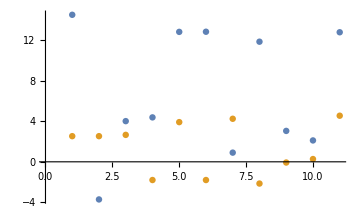

```mathematica
ListPlot[Transpose[pcdiffplot[[;;]]],ImageSize->Large]
```

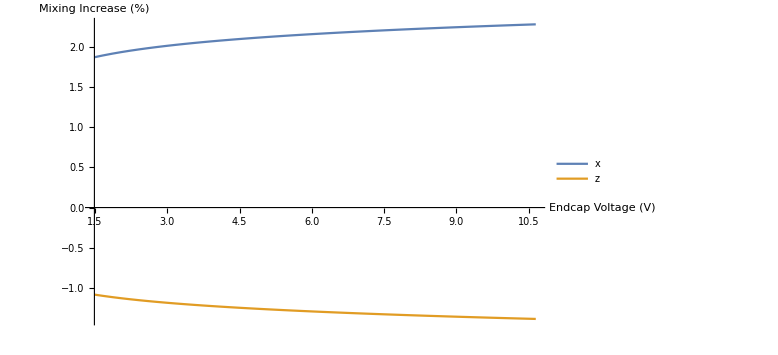
-Graphics-State: {3, 30, 8, 5}

```mathematica
(*as a function of U*)
statehold={3,30,8,5};

petKetstatehold=speed[statehold]*K^(1/12);
qrms2[d_,i_,ket_]:=Module[{holder=Simplify[rhatQ[d,i]·ket]},Sqrt[Simplify[SuperDagger[(holder)]·holder]]]
qrmspethold=Table[qrms2[d,i,petKetstatehold+stateToKet[statehold]],{d,2},{i,Num}]*K^(-0.25);
qrmsnormhold=Table[Sqrt[(gimnormRDX[[d,i]]^2/wmvalsnormRDX[[d]]/m[[i]]).If[d==1,statehold[[;;Num]]+0.5,statehold[[Num+1;;]]+0.5]],{d,2},{i,Num}]*K^(-0.25);
qrmsunpethold=Table[Sqrt[(gimRDX[[d,i]]^2/wmvalsRDX[[d]]/m[[i]]).If[d==1,statehold[[;;Num]]+0.5,statehold[[Num+1;;]]+0.5]],{d,2},{i,Num}]*K^(-0.25);

qrmsnormhold={Normalize[qrmsnormhold[[1]]],Normalize[qrmsnormhold[[2]]]};
qrmsunpethold={Normalize[qrmsunpethold[[1]]],Normalize[qrmsunpethold[[2]]]};
qrmspethold={Normalize[qrmspethold[[1]]],Normalize[qrmspethold[[2]]]};
pcdiffhold=100*{Norm[qrmsunpethold[[1]]-qrmsnormhold[[1]]]-Norm[qrmspethold[[1]]-qrmsnormhold[[1]]],Norm[qrmsunpethold[[2]]-qrmsnormhold[[2]]]-Norm[qrmspethold[[2]]-qrmsnormhold[[2]]]}//Simplify;

Labeled[Plot[Evaluate[pcdiffhold/.{K->K/1.488}],{K,1.488,10.65},ImageSize->Large,PlotLegends->{"x","z"},AxesLabel->{"Endcap Voltage (V)","Mixing Increase (%)"}],"State: " <> ToString[statehold],Top]
```

## 3 Calculate perturbed normal modes

## 3.1 Base functions

```mathematica
(*perturbation coefficients*)
cmnp[i_,j_,k_]:=Sum[(KroneckerDelta[i,j]-KroneckerDelta[di,j])*(KroneckerDelta[i,k]-KroneckerDelta[di,k])*Sign[di-i]*L0Mn[i,di,-4],{di,Num}];
Dijk[d_,i_,j_,k_]:=0.5*ke2/l0^4*Sum[cmnp[id,jd,kd]/Sqrt[m[[id]]*m[[jd]]*m[[kd]]]*gimmw[[3,id,i]]*gimmw[[d,jd,j]]*gimmw[[d,kd,k]],{id,Num},{jd,Num},{kd,Num}];

oVect[d_,i_,η0_]:=η0[[1,d,i]]*Exp[I*t*wmhz*wmvals[[d,i]]]+η0[[2,d,i]]*Exp[-I*t*wmhz*wmvals[[d,i]]];
petVect[d_,i_,η0_]:=3*Sum[Dijk[d,i,j,k]/wmhz^2*(If[d==1,2,-1]*(((η0[[1,3,k]]*η0[[1,d,j]])*Exp[I*t*wmhz*(wmvals[[3,k]]+wmvals[[d,j]])]+(η0[[2,3,k]]*η0[[2,d,j]])*Exp[-I*t*wmhz*(wmvals[[3,k]]+wmvals[[d,j]])])/(wmvals[[d,i]]^2-(wmvals[[3,k]]+wmvals[[d,j]])^2)+((η0[[1,3,k]]*η0[[2,d,j]])*Exp[I*t*wmhz*(wmvals[[3,k]]-wmvals[[d,j]])]+(η0[[2,3,k]]*η0[[1,d,j]])*Exp[-I*t*wmhz*(wmvals[[3,k]]-wmvals[[d,j]])])/(wmvals[[d,i]]^2-(wmvals[[3,k]]-wmvals[[d,j]])^2))-If[d==1,0,2*(((η0[[1,1,k]]*η0[[1,1,j]])*Exp[I*t*wmhz*(wmvals[[1,k]]+wmvals[[1,j]])]+(η0[[2,1,k]]*η0[[2,1,j]])*Exp[-I*t*wmhz*(wmvals[[3,k]]+wmvals[[3,j]])])/(wmvals[[3,i]]^2-(wmvals[[3,k]]+wmvals[[3,j]])^2)+((η0[[1,1,k]]*η0[[2,1,j]])*Exp[I*t*wmhz*(wmvals[[1,k]]-wmvals[[1,j]])]+(η0[[2,1,k]]*η0[[1,1,j]])*Exp[-I*t*wmhz*(wmvals[[1,k]]-wmvals[[1,j]])])/(wmvals[[1,i]]^2-(wmvals[[1,k]]-wmvals[[1,j]])^2))]),{j,Num},{k,Num}]//FullSimplify;
(*conversion*)
PosToη[q0_,v0_]:=Module[{A0,B0},
A0=Table[gimmw[[d]].(q0[[d]]*Sqrt[m]),{d,3}];B0=Table[gimmw[[d]].(v0[[d]]*Sqrt[m]/wmvals[[d]]/wmhz),{d,3}];
0.5*{A0-I*B0,A0+I*B0}
]

ModeToη[state_]:=5.79376459*^-21*(Sqrt[state/wmvals]+0.5);

ηToPos[eta_]:=Transpose

tRMS[func_,t1_,t2_]:=Sqrt[NIntegrate[Re[Evaluate[func]]^2,{t,t1,t2}]/(t2-t1)];

(*Plotting*)
plotExpr={"Unperturbed Mode", "Perturbation", "Perturbed Mode"};
getPetModes[d_,i_,eta0_]:=Module[{holder={oVect[d,i,eta0],petVect[d,i,eta0]}},Join[holder,{holder[[1]]+holder[[2]]}]];
```

## 3.2 Get results

```mathematica
qunits=1*^-9;vunits=1*^-6;
(*initialq={{200,200},{0,0},{200,200}}*qunits;initialv={{0,0},{0,0},{0,0}}*vunits;initialCond=PosToη[initialq,initialv];*)
icRange={{5,5},{5,5}};
initialCond=Table[Append[{ModeToη[{{x1,x2},{0,0},{z1,z2}}]},{{0,0},{0,0},{0,0}}],{x1,0,icRange[[1,1]]},{x2,0,icRange[[1,2]]},{z1,0,icRange[[2,1]]},{z2,0,icRange[[2,2]]}];
ηperturbed=ParallelTable[getPetModes[d,i,initialCond[[x1,x2,z1,z2]]],{x1,icRange[[1,1]]+1},{x2,icRange[[1,2]]+1},{z1,icRange[[2,1]]+1},{z2,icRange[[2,2]]+1},{d,3},{i,Num}];
```

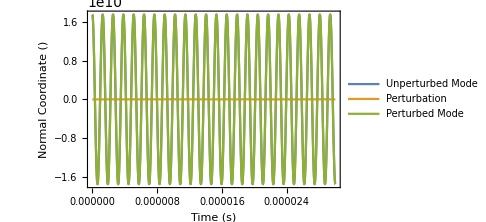
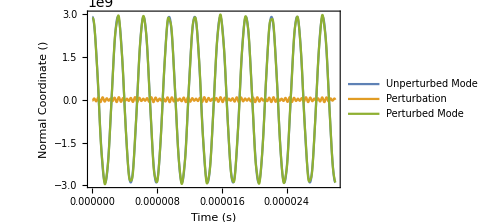
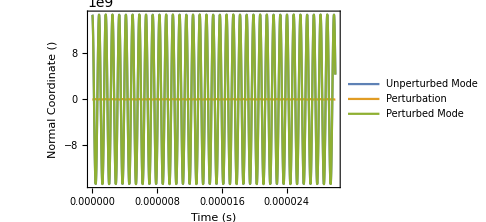
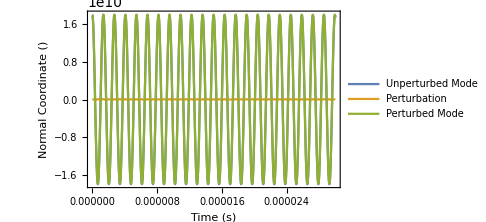

```mathematica
(*Plot!*)
tmax=30*2*Pi/wmhz;scaling=1*^30;
stateDJ={{5,0},{5,5}}+1;
Table[Plot[Evaluate[Re[Extract[ηperturbed,Flatten[Join[stateDJ,{d,i}]]]]*1],{t,0,tmax},PlotLegends->plotExpr,ImageSize->Medium,Frame->True,FrameLabel->{"Time (s)","Normal Coordinate ()"}],{d,1,3,2},{i,Num}]
```

```mathematica
(*get rms (over time) of perturbed states*)
ηtrms=ParallelTable[tRMS[ηperturbed[[x1,x2,z1,z2,d,i,j]],0,5*tmax],{x1,icRange[[1,1]]+1},{x2,icRange[[1,2]]+1},{z1,icRange[[2,1]]+1},{z2,icRange[[2,2]]+1},{d,3},{i,Num},{j,3}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000205055}. NIntegrate obtained 1.22026×10^-53 and 7.42626×10^-58 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000310524}. NIntegrate obtained 1.91587×10^-52 and 1.30473×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000266578}. NIntegrate obtained 3.31107×10^-52 and 2.24697×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000372047}. NIntegrate obtained 3.98133×10^-52 and 2.70497×10^-56 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000310524}. NIntegrate obtained 3.31751×10^-52 and 2.15269×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000310524}. NIntegrate obtained 5.42855×10^-51 and 3.78684×10^-55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000372047}. NIntegrate obtained 9.38942×10^-51 and 6.55535×10^-55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000372047}. NIntegrate obtained 1.12919×10^-50 and 7.88444×10^-55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000310524}. NIntegrate obtained 1.16358×10^-53 and 2.42268×10^-58 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000143531}. NIntegrate obtained 1.79519×10^-51 and 1.36953×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000143531}. NIntegrate obtained 5.30903×10^-51 and 3.99993×10^-56 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000805641}. NIntegrate obtained 7.65702×10^-51 and 5.80879×10^-56 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
pertRat=ηtrms[[;;,;;,;;,;;,;;,;;,3]]/ηtrms[[;;,;;,;;,;;,;;,;;,1]]-1;
```

```mathematica
pertRat[[1,1,6,6,1,;;]]*100
Max[pertRat]*100
```

{0.000058439,0.000736844}

0.972161

```mathematica
oVect[1,1,initialCondthermal]
```

6.83579×10^-20 ⅇ^((0.+4.92194×10^6 ⅈ) t)

```mathematica
initialCondthermal=Append[{ModeToη[{{100,0},{0,0},{100,100}}]},{{0,0},{0,0},{0,0}}]
ηthermal=Table[getPetModes[d,i,initialCondthermal],{d,3},{i,Num}];
```

{{{6.83579×10^-20,2.89688×10^-21},{2.89688×10^-21,2.89688×10^-21},{5.56383×10^-20,7.04926×10^-20}},{{0,0},{0,0},{0,0}}}

```mathematica
Table[tRMS[ηthermal[[d,i,3]],0,10*tmax]/tRMS[ηthermal[[d,i,1]],0,5*tmax]-1,{d,1,3,2},{i,Num}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.00022148}. NIntegrate obtained 7.0094×10^-43 and 6.903×10^-48 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0000902297}. NIntegrate obtained 1.39251×10^-45 and 3.77268×10^-48 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0001623}. NIntegrate obtained 4.64433×10^-43 and 2.09743×10^-46 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{3.12495×10^-6,0.0520221},{0.0000620433,-0.000186713}}

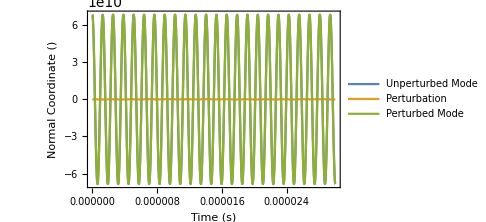
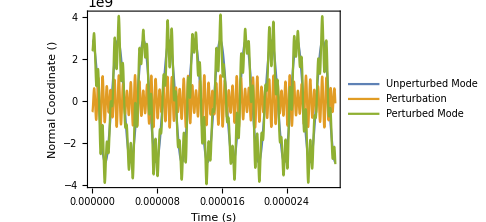
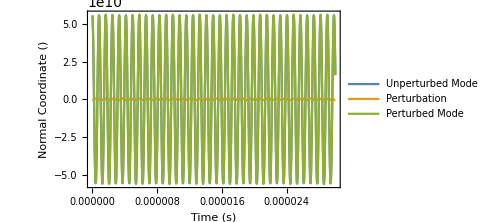
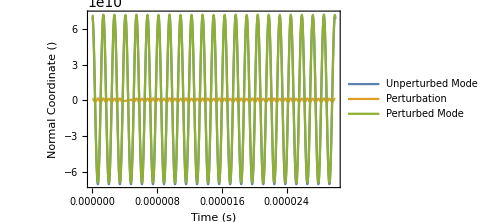

$Aborted

$Aborted

0.000105463 |0_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.000148484 |0_OverHat[1],0_OverHat[2],0_OverHat[3],2_OverHat[4]⟩+2.55187×10^-7 |0_OverHat[1],0_OverHat[2],0_OverHat[3],4_OverHat[4]⟩+0.000861098 |0_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-4.4173×10^-6 |0_OverHat[1],0_OverHat[2],1_OverHat[3],3_OverHat[4]⟩+0.0000551556 |0_OverHat[1],0_OverHat[2],2_OverHat[3],0_OverHat[4]⟩+0.000043363 |0_OverHat[1],0_OverHat[2],2_OverHat[3],2_OverHat[4]⟩-0.000218941 |0_OverHat[1],0_OverHat[2],3_OverHat[3],1_OverHat[4]⟩+0.00137905 |0_OverHat[1],2_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-0.000219612 |0_OverHat[1],2_OverHat[2],0_OverHat[3],2_OverHat[4]⟩+0.00158022 |0_OverHat[1],2_OverHat[2],1_OverHat[3],1_OverHat[4]⟩+0.000130154 |1_OverHat[1],1_OverHat[2],0_OverHat[3],0_OverHat[4]⟩+0.0000389773 |1_OverHat[1],1_OverHat[2],0_OverHat[3],2_OverHat[4]⟩-0.000306842 |1_OverHat[1],1_OverHat[2],1_OverHat[3],1_OverHat[4]⟩-6.85936×10^-6 |2_OverHat[1],0_OverHat[2],0_OverHat[3],0_OverHat[4]⟩-3.78017×10^-6 |2_OverHat[1],0_OverHat[2],0_OverHat[3],2_OverHat[4]⟩+0.0000313779 |2_OverHat[1],0_OverHat[2],1_OverHat[3],1_OverHat[4]⟩

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

```mathematica
Table[Plot[Evaluate[Re[ηthermal[[d,i]]]*scaling],{t,0,tmax},PlotLegends->plotExpr,ImageSize->Medium,Frame->True,FrameLabel->{"Time (s)","Normal Coordinate ()"}],{d,1,3,2},{i,Num}]
```